Preamble

## Package Imports

```mathematica
AppendTo[$Path,"C:\\Users\\Nilo\\__DATA\\Mega\\DATA\\eclipse-workspace2\\NumberTheory"];
<<NumberTheory`
```

```mathematica
ComplexAnalysis`BranchPoints[√(z^2-1),z]
ComplexAnalysis`BranchCuts[√(z^2-1),z]
```

{-1,1,ComplexInfinity}

(-1<Re[z]<0&&Im[z]==0)||Re[z]==0||(0<Re[z]<1&&Im[z]==0)

## Examples

### Definition / Theorem

This is text.

#### Example

# <OLD>

Complex Integration

## Contour Integral

### Definition / Theorem

#### Example

```mathematica
cContourIntegral[1/z,z,cPath[4]]//Expand
```

2 ⅈ π

## tmp

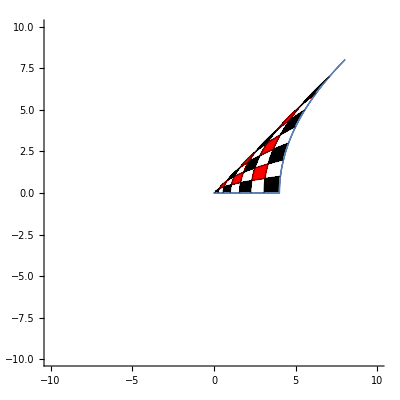

```mathematica
GraphicsRow[
With[{s=σ+I t},
ParametricPlot[{σ^2+t^2,2σ t},{σ,0,2},{t,0,2},
Frame->False,
Mesh->{7,7},
MeshShading->ArrayPad[{{None,Black},{Red,None}},{{0,0},{0,0}},None],
PlotRange->{{-10,10},{-10,10}}]
]&/@{Identity}]
```

```mathematica
(z-I Im[z])^2-(-I z+ I Re[z])^2+2I (z-I Im[z])(-I z+ I Re[z])//FullSimplify
```

z^2

```mathematica
((z-I Im[z])^2+(-I z+ I Re[z])^2+2I (z-I Im[z])(-I z+ I Re[z])//FullSimplify)/.z:>"#"
```

1/2 (#^2+2 # Conjugate[#]-Conjugate[#]^2)

```mathematica
(z-I Im[z])^2-(-I z+ I Re[z])^2-2I (z-I Im[z])(-I z+ I Re[z])//FullSimplify
```

Conjugate[z]^2

```mathematica
D[ComplexExpand[Re[(x+I y)^2]],{x,1}]
D[ComplexExpand[Im[(x+I y)^2]],{y,1}]
D[ComplexExpand[Re[(x+I y)^2]],{y,1}]
-D[ComplexExpand[Im[(x+I y)^2]],{x,1}]
```

2 x

2 x

-2 y

-2 y

```mathematica
D[ComplexExpand[Re[Conjugate[(x+I y)]^2]],{x,1}]
D[ComplexExpand[Im[Conjugate[(x+I y)]^2]],{y,1}]
D[ComplexExpand[Re[Conjugate[(x+I y)]^2]],{y,1}]
-D[ComplexExpand[Im[Conjugate[(x+I y)]^2]],{x,1}]
```

2 x

-2 x

-2 y

2 y

Visualizations

## Visualize Function

## Test-0

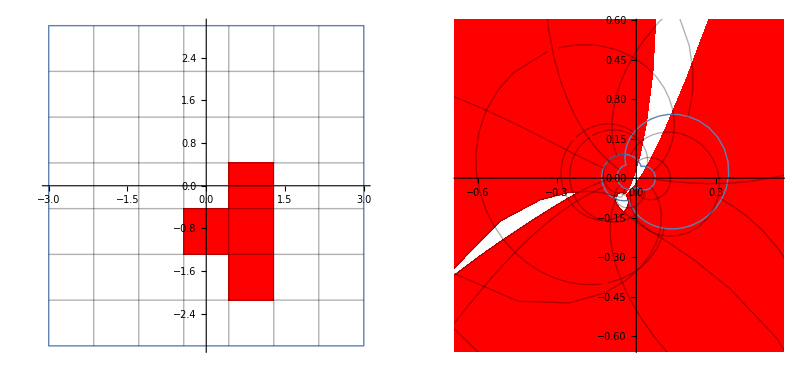

```mathematica
ClearAll[t1,t2,r1,r2,dt,dr]
F[z_]:=Gamma[z]
F[z_]:=WeierstrassP[z,WeierstrassInvariants[{1,I}]]
F[z_]:=(z+I)/(z^2(z-2))
r1=-3;
r2=3;
t1=-3;
t2=3;
GraphicsRow[
With[{z=r + I t,col=Red},
ParametricPlot[ReIm@#[z],{r,r1,r2},{t,t1,t2},
Mesh->6,
MeshShading->ArrayPad[{{None,col},{col,col},{None,col}},{{1,5},{3,5}},None],
Frame->False,
AxesOrigin->{0,0}]]&/@{Identity,F}]
```

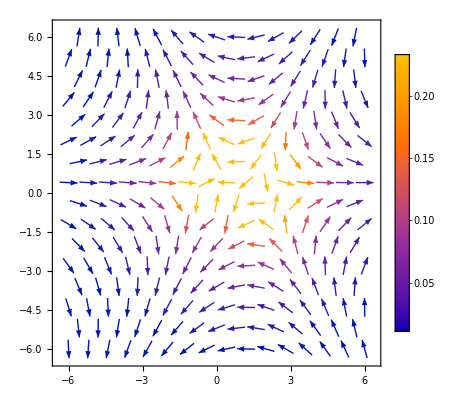

```mathematica
ComplexVectorPlot[F[z],{z,-6-6I,6+6I},PlotLegends->Automatic]
```

## Test-1

```mathematica
f[s_]:=2s
GraphicsRow[
With[{s=σ+I t},
ParametricPlot[ReIm@#[s],{x,0,4},{y,0,8}]
]&/@{Identity,f}]
```

-Graphics-

## Test-2

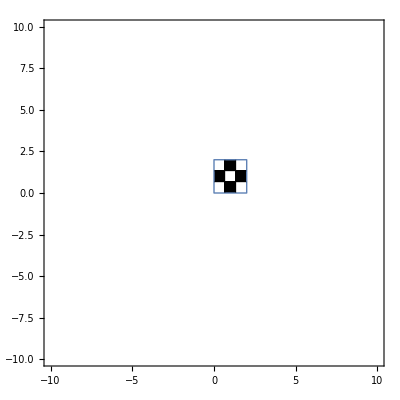

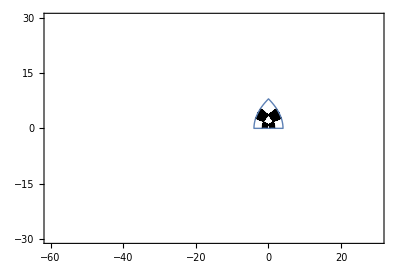

```mathematica
With[{s=σ+I t},
ParametricPlot[ReIm[s],{σ,0,2},{t,0,2},
Mesh->{2,2},
MeshShading->ArrayPad[{{None,Black},{Black,None}},{{0,0},{0,0}},None],
PlotRange->{{-10,10},{-10,10}}]
]
With[{s=σ+I t},
ParametricPlot[ReIm[s^2],{σ,0,2},{t,0,2},
Mesh->{2,2},
MeshShading->ArrayPad[{{None,Black},{Black,None}},{{0,0},{0,0}},None],
PlotRange->{{-60,30},{-30,30}}]
]
```

## Test-3

### Demo-1

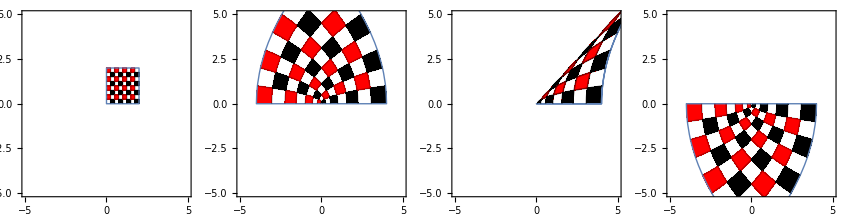

```mathematica
GraphicsRow[
With[{s=σ+I t},
ParametricPlot[ReIm@#[s],{σ,0,2},{t,0,2},
Axes->{True,True},
Frame->True,
Mesh->{7,7},
MeshShading->ArrayPad[{{None,Black},{Red,None}},{{0,0},{0,0}},None],
PlotRange->{{-5,5},{-5,5}}]
]&/@{Identity,#^2&,1/2 (#^2+2 # Conjugate[#]-Conjugate[#]^2)&,Conjugate[#]^2&}]
```

### Demo-2

```mathematica
GraphicsRow[
With[{s=σ+I t},
ParametricPlot[ReIm@#[s],{σ,0,1},{t,0,1},
Axes->{True,True},
Frame->True,
Mesh->{7,7},
MeshShading->ArrayPad[{{None,Black},{Red,None}},{{0,0},{0,0}},None],
PlotRange->{{-5,5},{-5,5}}]
]&/@{Identity,WeierstrassP[#,{0,1}]&,WeierstrassP[#,{1,0}]&}]
```

### Problem-1: Weierstrass-p is an even function : How to explain the following graphs below

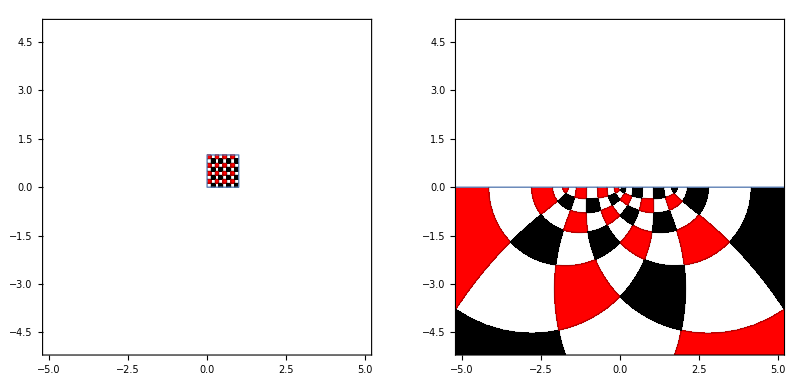

```mathematica
GraphicsRow[
With[{s=σ+I t},
ParametricPlot[ReIm@#[s],{σ,0,1},{t,0,1},
Axes->{True,True},
Frame->True,
Mesh->{7,7},
MeshShading->ArrayPad[{{None,Black},{Red,None}},{{0,0},{0,0}},None],
PlotRange->{{-5,5},{-5,5}}]
]&/@{Identity,WeierstrassP[#,WeierstrassInvariants[{1,I}]]&}]
```

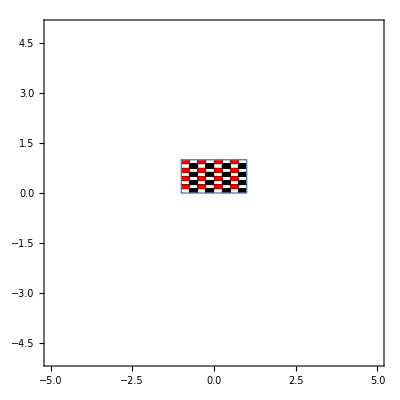

```mathematica
GraphicsRow[
With[{s=σ+I t},
ParametricPlot[ReIm@#[s],{σ,-1,1},{t,0,1},
Axes->{True,True},
Frame->True,
Mesh->{7,7},
MeshShading->ArrayPad[{{None,Black},{Red,None}},{{0,0},{0,0}},None],
PlotRange->{{-5,5},{-5,5}}]
]&/@{Identity,WeierstrassP[#,WeierstrassInvariants[{1,I}]]&}]
```

```mathematica
ComplexPlot3D[WeierstrassP[z,WeierstrassInvariants[{2,2I}]],{z,0,10+10I},PlotLegends->Automatic]
```

Power::infy: Infinite expression 1/(0.+0. ⅈ)^2 encountered.

-Graphics3D-

```mathematica
WeierstrassInvariants[{1,I}]//N
```

{11.817+0. ⅈ,2.15808×10^-15+0. ⅈ}

### Demo-3

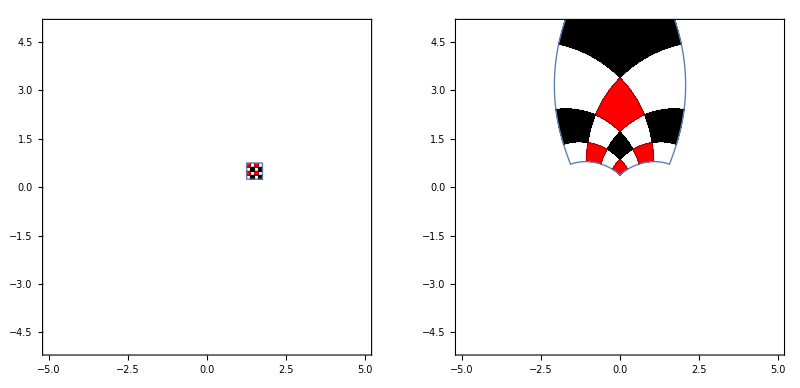

```mathematica
GraphicsRow[
With[{s=σ+I t},
ParametricPlot[ReIm@#[s],{σ,1.25,1.75},{t,0.25,0.75},
Axes->{True,True},
Frame->True,
Mesh->{3,3},
MeshShading->ArrayPad[{{None,Black},{Red,None}},{{0,0},{0,0}},None],
PlotRange->{{-5,5},{-5,5}}]
]&/@{Identity,WeierstrassP[#,WeierstrassInvariants[{1,I}]]&}]
```

### tmp

```mathematica
{Identity,#^2&,Gamma[#]&,PolyGamma[0,#]&,Log[#]&}
```

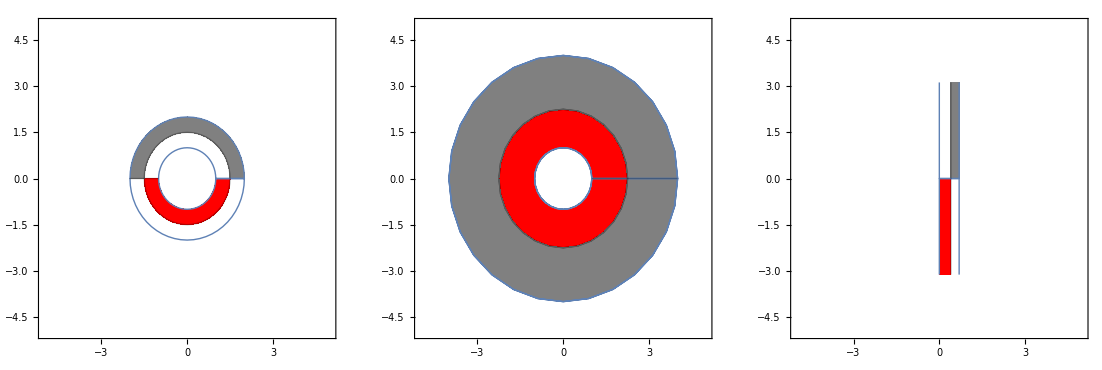

```mathematica
GraphicsRow[
With[{s=r Exp[I t]},
ParametricPlot[ReIm@#[s],{r,1,2},{t,0, 4π/2},
Axes->{True,True},
Frame->True,
Mesh->{1,1},
MeshShading->ArrayPad[{{None,Gray},{Red,None}},{{0,0},{0,0}},None],
PlotRange->{{-5,5},{-5,5}}]
]&/@{Identity,#^2&,Log[#]&}]
```

### tmp-1

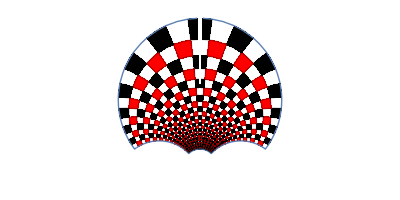

```mathematica
GraphicsRow[
With[{s=σ+I t},
ParametricPlot[ReIm@#[s],{σ,-2,2},{t,1,5},
Axes->{False,False},
Frame->False,
Mesh->{26,26},
MeshShading->ArrayPad[{{None,Black},{Red,None}},{{0,0},{0,0}},None],
PlotRange->{{-1,1},{0,1}}]
]&/@{-1/#&}]
```

```mathematica
{Identity,WeierstrassP[#,WeierstrassInvariants[{1,I}]]+I&,-1/(WeierstrassP[#,WeierstrassInvariants[{1,I}]]+I)&}
```

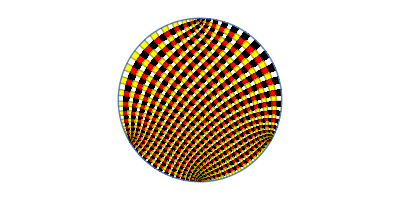

```mathematica
GraphicsRow[
With[{s=σ+I t},
ParametricPlot[ReIm@#[s],{σ,1,2},{t,0,1},
Axes->{False,False},
Frame->False,
Mesh->{40,40},
MeshShading->ArrayPad[{{None,Black},{Yellow,Red}},{{0,0},{0,0}},None],
PlotRange->{{-1,1},{0,1}}]
]&/@{-1/(WeierstrassP[#,WeierstrassInvariants[{1,I}]]+I)&}]
```

## Test-4

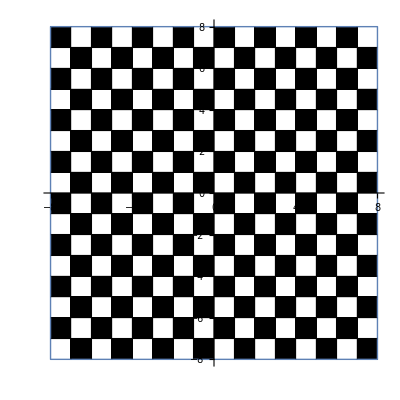

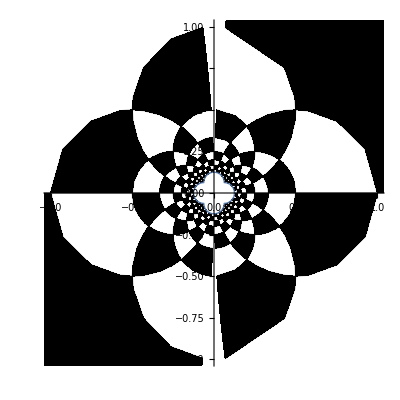

```mathematica
F[z_]:=1/z
r1=-8;
r2=8;
t1=-8;
t2=8;
GraphicsRow[
With[{z=r +I t,col=Black},
ParametricPlot[ReIm@#[z],{r,r1,r2},{t,t1,t2},
Mesh->15,
MeshShading->{{None,col},{col,None}},
Frame->False,AxesOrigin->{0,0},PlotRange->{{-8,8},{-8,8}}]
]&/@{Identity}]
GraphicsRow[
With[{z=r +I t,col=Black},
ParametricPlot[ReIm@#[z],{r,r1,r2},{t,t1,t2},
Mesh->15,
MeshShading->{{None,col},{col,None}},
Frame->False,AxesOrigin->{0,0},PlotRange->{{-1,1},{-1,1}}]
]&/@{F}]
```

```mathematica
|
```

```mathematica
√(1+I)//N
```

1.09868+0.45509 ⅈ

```mathematica
(-1.0986841134678098-0.45508986056222733 ⅈ)^2
```

1.+1. ⅈ

```mathematica
(-1.0986841134678098-0.45508986056222733 ⅈ)^2
```

1.+1. ⅈ

```mathematica
Import["http://www.mathematicaguidebooks.org/V6/downloads/RiemannSurfacePlot3D.m"]
rsurf[func_]:=Grid[{
{RiemannSurfacePlot3D[w==func,Re[w],{z,w},ImageSize->400,Coloring->Hue[Rescale[ArcTan[1.4 Im[w]],{-Pi/2,Pi/2}]],PlotPoints->{40,40},Boxed->False],RiemannSurfacePlot3D[w==func,Im[w],{z,w},ImageSize->400,Coloring->Hue[Rescale[ArcTan[1.4 Re[w]],{-Pi/2,Pi/2}]],PlotPoints->{40,40},Boxed->False]}}];
```

```mathematica
rsurf/@{Log[z]}
```

{-Graphics3D- | -Graphics3D-}

```mathematica
Series[Cos[z],{z,0,12}]//Normal
```

1-z^2/2+z^4/24-z^6/720+z^8/40320-z^10/3628800+z^12/479001600

## tmp

```mathematica
f[z_]:=√Abs[z] ⅇ^(1/2 ⅈ Arg[z])
g[z_]:=√z
```

```mathematica
g[I]//N
(-g[-I])//N

g[I]^2//N
(g[-I])^2//N
```

0.707107+0.707107 ⅈ

-0.707107+0.707107 ⅈ

0.+1. ⅈ

0.-1. ⅈ

```mathematica
Import["http://www.mathematicaguidebooks.org/V6/downloads/RiemannSurfacePlot3D.m"]
rsurf[func_]:=Grid[{
{RiemannSurfacePlot3D[w==func,Re[w],{z,w},ImageSize->400,Coloring->Hue[Rescale[ArcTan[1.4 Im[w]],{-Pi/2,Pi/2}]],PlotPoints->{40,40},Boxed->False],RiemannSurfacePlot3D[w==func,Im[w],{z,w},ImageSize->400,Coloring->Hue[Rescale[ArcTan[1.4 Re[w]],{-Pi/2,Pi/2}]],PlotPoints->{40,40},Boxed->False]}}];
```

```mathematica
rsurf/@{Sqrt[z]}
```

{-Graphics3D- | -Graphics3D-}

```mathematica
Solve[ⅇ^((z^2-5)/z)==√2,z]/.C[1]->1
f[z_]:=ⅇ^((z^2-5)/z)
f[1/2 (2 ⅈ π-√(20+(2 ⅈ π+Log[2]/2)^2)+Log[2]/2)]//FullSimplify
```

{{z→1/2 (2 ⅈ π-√(20+(2 ⅈ π+Log[2]/2)^2)+Log[2]/2)},{z→1/2 (2 ⅈ π+√(20+(2 ⅈ π+Log[2]/2)^2)+Log[2]/2)}}

√2

```mathematica
Series[ ⅇ^(1/z),{z,Infinity,10}]
```

1+1/z+1/(2 z^2)+1/(6 z^3)+1/(24 z^4)+1/(120 z^5)+1/(720 z^6)+1/(5040 z^7)+1/(40320 z^8)+1/(362880 z^9)+1/(3628800 z^10)+O[1/z]^11

```mathematica
Series[ z Cos[1/z],{z,Infinity,10}]
```

z-1/(2 z)+1/(24 z^3)-1/(720 z^5)+1/(40320 z^7)-1/(3628800 z^9)+O[1/z]^11

```mathematica
Series[ z^2 Sin[1/z]Cosh[1/z],{z,Infinity,10}]
```

z+1/(3 z)-1/(30 z^3)-1/(630 z^5)+1/(22680 z^7)+1/(1247400 z^9)+O[1/z]^11

```mathematica
Integrate[Tan[x],x]
```

-Log[Cos[x]]

```mathematica
Integrate[Sin[x]/x,x]
```

```mathematica
Series[SinIntegral[x],{x,0,10}]
```

x-x^3/18+x^5/600-x^7/35280+x^9/3265920+O[x]^11

```mathematica
Sum[((-1)^k z^(2k))/((1+2k)^2 (2k)!), {k, 0, Infinity}]//FullSimplify
```

SinIntegral[z]/z

```mathematica
Series[Cos[z]/z,{z,0,11}]
Integrate[Cos[z]/z,z]
```

1/z-z/2+z^3/24-z^5/720+z^7/40320-z^9/3628800+z^11/479001600+O[z]^12

CosIntegral[z]

```mathematica
ComplexPlot3D[CosIntegral[z],{z,-2-2I,2+2I},PlotLegends->Automatic]
```

-Graphics3D-

# Notes Complex Analysis

7. Power Series

## Taylor Series

### Examples

```mathematica
Series[Sin[z],{z,0,15}]
```

z-z^3/6+z^5/120-z^7/5040+z^9/362880-z^11/39916800+z^13/6227020800-z^15/1307674368000+O[z]^16

```mathematica
Series[Sin[z^2],{z,0,30}]
```

z^2-z^6/6+z^10/120-z^14/5040+z^18/362880-z^22/39916800+z^26/6227020800-z^30/1307674368000+O[z]^31

```mathematica
Series[ArcSin[z],{z,0,15}]
```

z+z^3/6+(3 z^5)/40+(5 z^7)/112+(35 z^9)/1152+(63 z^11)/2816+(231 z^13)/13312+(143 z^15)/10240+O[z]^16

```mathematica
Series[Tan[z],{z,0,15}]
```

z+z^3/3+(2 z^5)/15+(17 z^7)/315+(62 z^9)/2835+(1382 z^11)/155925+(21844 z^13)/6081075+(929569 z^15)/638512875+O[z]^16

```mathematica
Series[Log[1+z],{z,0,15}]
```

z-z^2/2+z^3/3-z^4/4+z^5/5-z^6/6+z^7/7-z^8/8+z^9/9-z^10/10+z^11/11-z^12/12+z^13/13-z^14/14+z^15/15+O[z]^16

## Laurent Series

## Infinite Products

12. Gamma, Beta and Zeta Functions

## Gamma Function

### Definition

```mathematica
gamma[z_]:=Integrate[t^(z-1)ⅇ^-t,{t,0,Infinity},Assumptions->{Re[z]>0}]
```

### Specific Values

```mathematica
Table[gamma[(k+1)/2],{k,0,9}]
Table[Gamma[(k+1)/2],{k,0,9}]
Table[Gamma[(k+1)/2],{k,-9,0}]
```

{√π,1,(√π)/2,1,(3 √π)/4,2,(15 √π)/8,6,(105 √π)/16,24}

{√π,1,(√π)/2,1,(3 √π)/4,2,(15 √π)/8,6,(105 √π)/16,24}

{ComplexInfinity,(16 √π)/105,ComplexInfinity,-(8 √π)/15,ComplexInfinity,(4 √π)/3,ComplexInfinity,-2 √π,ComplexInfinity,√π}

### Derivative

```mathematica
Limit[(gamma[z+h]-gamma[z])/h,h->0]
D[Gamma[z],{z,1}]
Integrate[D[t^(z-1)ⅇ^-t,{z,1}],{t,0,Infinity},Assumptions->{Re[z]>0}]
```

Gamma[z] PolyGamma[0,z]

Gamma[z] PolyGamma[0,z]

Gamma[z] PolyGamma[0,z]

```mathematica
D[Gamma[z],{z,1}]/.z->1
```

-EulerGamma

```mathematica
(D[Gamma[z],{z,2}]//FunctionExpand)/.z->1
```

EulerGamma^2+π^2/6

### Functional Equations

```mathematica
Gamma[z+1]==z Gamma[z]//FunctionExpand
```

True

```mathematica
Gamma[z]==Gamma[z+k]/Pochhammer[z,k]//FunctionExpand
```

True

```mathematica
Gamma[z]Gamma[1-z]==π/Sin[π z]//FunctionExpand
```

True

```mathematica
Gamma[z]==(2 π)^(-1/2)2^(z-1/2)Gamma[z/2]Gamma[(z+1)/2]//FunctionExpand
```

True

## Eta Function

### Definition

### Convergence

The eta function converges for Re(s) > 0.

## Zeta Function

### Definition

```mathematica
zeta[z_]:=Sum[k^-z,{k,1,Infinity}]
zeta[2+2I]//N
Zeta[2+2I]//N
```

0.867352-0.275127 ⅈ

0.867352-0.275127 ⅈ

### Analytic Continuation of Zeta

```mathematica
zeta[-3]
Zeta[-3]
```

Sum::div: Sum does not converge.

∑_(k=1)^∞ k^3

1/120

13. Special Functions

## Bessel Function

### Definition

```mathematica
DSolve[{z^2 w''[z]+z w'[z]+(z^2-a^2)w[z]==0}, w[z], z]
```

{{w[z]→BesselJ[a,z] C[1]+BesselY[a,z] C[2]}}

```mathematica
Series[BesselJ[0,z],{z,0,16}]
Series[BesselJ[1,z],{z,0,16}]
Series[BesselY[0,z],{z,0,5}]
Series[BesselY[1,z],{z,0,5}]
```

1-z^2/4+z^4/64-z^6/2304+z^8/147456-z^10/14745600+z^12/2123366400-z^14/416179814400+z^16/106542032486400+O[z]^17

z/2-z^3/16+z^5/384-z^7/18432+z^9/1474560-z^11/176947200+z^13/29727129600-z^15/6658877030400+O[z]^17

(2 (EulerGamma-Log[2]+Log[z]))/π+((1-EulerGamma+Log[2]-Log[z]) z^2)/(2 π)+((-3+2 EulerGamma-2 Log[2]+2 Log[z]) z^4)/(64 π)+O[z]^6

-2/(π z)+((-1+2 EulerGamma-2 Log[2]+2 Log[z]) z)/(2 π)+((5-4 EulerGamma+4 Log[2]-4 Log[z]) z^3)/(32 π)+((-5+3 EulerGamma-3 Log[2]+3 Log[z]) z^5)/(576 π)+O[z]^6